### Setting up board

#### Getters

```mathematica
getTileType[board_,sector_,row_,column_]:=board⟦sector,row,column,1⟧
```

```mathematica
getTilePoints[board_,sector_,row_,column_]:=board⟦sector,row,column,2⟧
```

```mathematica
getNeighborPos[board_,sector_,row_,column_]:=board⟦sector,row,column,3⟧
```

```mathematica
(*Returns tile data for structured board*)
getTile[board_,listPos_]:=board⟦listPos⟦1⟧,listPos⟦2⟧,listPos⟦3⟧⟧
```

#### Mine setup

```mathematica
(*This method returns a board without the primitives, just if its a mine or not*)
setupMines[numOfRows_,factor_]:= 
Module[
{tiles = 8*numOfRows^2 ,
lst = Table[{},{x,1,8}],
row,section,
numOfTiles,remainingMineCount,tile},
remainingMineCount = factor * tiles;
(*For loop for stacking *)
For[row = 1,row≤ numOfRows,row++,
(*Goes through each section*)
For[section = 1, section≤ 8, section++,
AppendTo[lst⟦section⟧,{}];
(*Loop to add tiles to each section & row*)
For[numOfTiles= 1, numOfTiles≤ 2*row - 1,numOfTiles++,
tile = RandomChoice[{remainingMineCount/tiles,(tiles - remainingMineCount)/tiles}->{Red,Blue}];
If[tile == Red,
remainingMineCount--;
];
tiles--;
AppendTo[lst⟦section⟧⟦row⟧,tile]
]
]
];
Return [lst]
]
```

```mathematica
Grid[boardSetUp[3,0.25]]
```

{RGBColor[0, 0, 1]} | {RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1]} | {RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0]}
{RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1]} | {RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]}
{RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1]} | {RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]}
{RGBColor[0, 0, 1]} | {RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0]} | {RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1]}
{RGBColor[0, 0, 1]} | {RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]} | {RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1]}
{RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1]} | {RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]}
{RGBColor[1, 0, 0]} | {RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]} | {RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]}
{RGBColor[0, 0, 1]} | {RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1]} | {RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 0, 1]}

#### Triangle point setup

Setting up coordinates of triangles.

```mathematica
(*Construct a single row of triangles for the tiling*)
constructTiledTriangleRow[numItems_,offset_]:=Module[
{(*This constructs the zigzag shape of the triangles*)
zigzag=Riffle[
Table[N@{pointX,Sin[(3π)/8]}+offset,{pointX,-(numItems+1)/2 Cos[(3π)/8],(numItems+1)/2 Cos[(3π)/8],2Cos[(3π)/8]}],
Table[N@{pointX,0}+offset,{pointX,-(numItems-1)/2 Cos[(3π)/8],(numItems-1)/2 Cos[(3π)/8],2Cos[(3π)/8]}]

]
},
(*Take advantage of the zigzag shape to construct triangles*)
Return[Table[{zigzag⟦i⟧,zigzag⟦i+1⟧,zigzag⟦i+2⟧},{i,numItems}]]
]
```

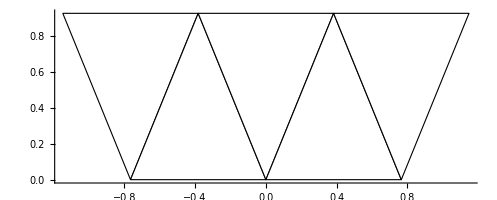

```mathematica
Graphics[{EdgeForm[{Thickness[Large],Black}],White,Triangle[constructTiledTriangleRow[5,{0,0}]]},Axes->True]
```

```mathematica
(*Constructs a "big" triangle*)
constructTiledTriangle[numRows_]:=Table[constructTiledTriangleRow[numTriangles,{0,(numTriangles-1)/2*Sin[(3π)/8]}],{numTriangles,1,2numRows-1,2}]
```

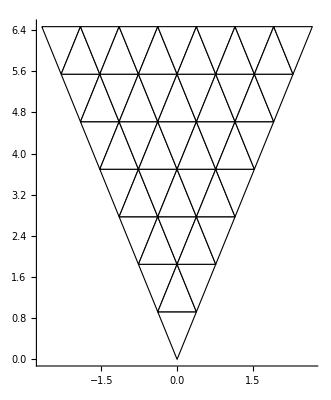

```mathematica
Graphics[{EdgeForm[{Thickness[Large],Black}],White,Triangle[Join@@constructTiledTriangle[7]]},Axes->True]
```

```mathematica
(*Rotate points of a triangle created from constructTiledTriangle*)
rotateMassTriangle[triangles_,θ_]:=Table[Table[Table[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}.point,{point,triangle}],{triangle,row}],{row,triangles}]
```

```mathematica
(*Construct triangle points for the board tiles.
The return structure is structured the same way as a regular board, except this only gives tile corner coordinates
*)
createBoardSkeleton[numRows_]:=Table[rotateMassTriangle[constructTiledTriangle[numRows],θ],{θ,2π,π/4,-π/4}]
```

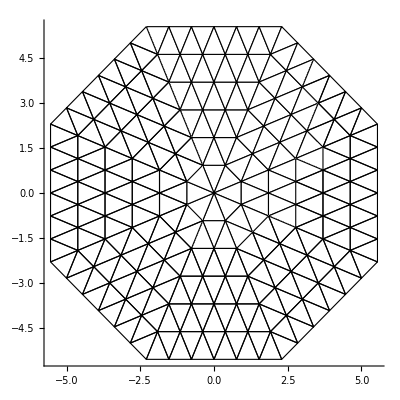

```mathematica
Graphics[{EdgeForm[{Thickness[Large],Black}],White,Triangle[Join@@Join@@createBoardSkeleton[6]]},Axes->True]
```

#### Neighbors setup (casework)

We can split this into 3 general cases:
 * Adjacency within big triangles
 * Adjacency between big triangles
 * Adjacency from torus connections
There is one more case, however - the central 8 triangles
Is there a better way to do this?

```mathematica
(*Error checking to ensure we do not add any invalid neighbors. Less cases to handle manually*)
SetAttributes[addNeighbor,HoldFirst]
addNeighbor[neighborLst_,numRows_,sector_,row_,tile_]:=
If[1≤sector≤8&&1≤row≤numRows&&1≤tile≤2*row-1&&!MemberQ[neighborLst,{sector,row,tile}],AppendTo[neighborLst,{sector,row,tile}]
]
```

```mathematica
SetAttributes[getAdjacentBigTriangle,HoldFirst]
getAdjacentBigTriangle[neighborsPoints_,numRows_,sector_,row_,tile_]:=Module[{},
(*Left side*)
If[tile<=2,
addNeighbor[neighborsPoints,numRows,Mod[sector-2,8]+1,row,2*row-1];
addNeighbor[neighborsPoints,numRows,Mod[sector-2,8]+1,row,2*row-2];
addNeighbor[neighborsPoints,numRows,Mod[sector-2,8]+1,row-1,2*(row-1)-1];
If[tile==1,
addNeighbor[neighborsPoints,numRows,Mod[sector-2,8]+1,row+1,2*(row+1)-1];
addNeighbor[neighborsPoints,numRows,Mod[sector-2,8]+1,row+1,2*(row+1)-2];
]
];
(*Right side*)
If[tile≥2*row-2,
addNeighbor[neighborsPoints,numRows,Mod[sector-1,8]+2,row,1];
addNeighbor[neighborsPoints,numRows,Mod[sector-1,8]+2,row,2];
addNeighbor[neighborsPoints,numRows,Mod[sector-1,8]+2,row-1,1];
If[tile==1,
addNeighbor[neighborsPoints,numRows,Mod[sector-1,8]+2,row+1,1];
addNeighbor[neighborsPoints,numRows,Mod[sector-1,8]+2,row+1,2];
]
]
]
```

```mathematica
(*Find neighbors of tile*)
figureOutNeighbors[numRows_,sector_,row_,tile_]:=Module[
{neighborsPoints={}},
(*Handle special central case*)
If[row==1,
Do[
If[currSector≠sector,addNeighbor[neighborsPoints,numRows,sector,row,tile]]
,{currSector,1,8}
]
];
(*Handle adjacency inside triangle*)
(*Handle adjacency between big triangles*)
getAdjacentBigTriangle[neighborsPoints,numRows,sector,row,tile];
(*Handle adjacency from outer edge connection*)
Return[neighborsPoints]
]
```

```mathematica
setupNeighbors[numRows_]:=
Table[
Table[
Table[
figureOutNeighbors[numRows,sector,row,tile]
,{tile,2*row-1}
]
,{row,numRows}
]
,{sector,1,8}
]
```

```mathematica
setupNeighbors[5]
```

{{{{{1,1,1},{8,1,1},{8,2,3},{8,2,2},{2,1,1},{2,2,1},{2,2,2}}},{{{8,2,3},{8,2,2},{8,1,1},{8,3,5},{8,3,4}},{{8,2,3},{8,2,2},{8,1,1},{2,2,1},{2,2,2},{2,1,1}},{{2,2,1},{2,2,2},{2,1,1}}},{{{8,3,5},{8,3,4},{8,2,3},{8,4,7},{8,4,6}},{{8,3,5},{8,3,4},{8,2,3}},{},{{2,3,1},{2,3,2},{2,2,1}},{{2,3,1},{2,3,2},{2,2,1}}},{{{8,4,7},{8,4,6},{8,3,5},{8,5,9},{8,5,8}},{{8,4,7},{8,4,6},{8,3,5}},{},{},{},{{2,4,1},{2,4,2},{2,3,1}},{{2,4,1},{2,4,2},{2,3,1}}},{{{8,5,9},{8,5,8},{8,4,7}},{{8,5,9},{8,5,8},{8,4,7}},{},{},{},{},{},{{2,5,1},{2,5,2},{2,4,1}},{{2,5,1},{2,5,2},{2,4,1}}}},{{{{2,1,1},{1,1,1},{1,2,3},{1,2,2},{3,1,1},{3,2,1},{3,2,2}}},{{{1,2,3},{1,2,2},{1,1,1},{1,3,5},{1,3,4}},{{1,2,3},{1,2,2},{1,1,1},{3,2,1},{3,2,2},{3,1,1}},{{3,2,1},{3,2,2},{3,1,1}}},{{{1,3,5},{1,3,4},{1,2,3},{1,4,7},{1,4,6}},{{1,3,5},{1,3,4},{1,2,3}},{},{{3,3,1},{3,3,2},{3,2,1}},{{3,3,1},{3,3,2},{3,2,1}}},{{{1,4,7},{1,4,6},{1,3,5},{1,5,9},{1,5,8}},{{1,4,7},{1,4,6},{1,3,5}},{},{},{},{{3,4,1},{3,4,2},{3,3,1}},{{3,4,1},{3,4,2},{3,3,1}}},{{{1,5,9},{1,5,8},{1,4,7}},{{1,5,9},{1,5,8},{1,4,7}},{},{},{},{},{},{{3,5,1},{3,5,2},{3,4,1}},{{3,5,1},{3,5,2},{3,4,1}}}},{{{{3,1,1},{2,1,1},{2,2,3},{2,2,2},{4,1,1},{4,2,1},{4,2,2}}},{{{2,2,3},{2,2,2},{2,1,1},{2,3,5},{2,3,4}},{{2,2,3},{2,2,2},{2,1,1},{4,2,1},{4,2,2},{4,1,1}},{{4,2,1},{4,2,2},{4,1,1}}},{{{2,3,5},{2,3,4},{2,2,3},{2,4,7},{2,4,6}},{{2,3,5},{2,3,4},{2,2,3}},{},{{4,3,1},{4,3,2},{4,2,1}},{{4,3,1},{4,3,2},{4,2,1}}},{{{2,4,7},{2,4,6},{2,3,5},{2,5,9},{2,5,8}},{{2,4,7},{2,4,6},{2,3,5}},{},{},{},{{4,4,1},{4,4,2},{4,3,1}},{{4,4,1},{4,4,2},{4,3,1}}},{{{2,5,9},{2,5,8},{2,4,7}},{{2,5,9},{2,5,8},{2,4,7}},{},{},{},{},{},{{4,5,1},{4,5,2},{4,4,1}},{{4,5,1},{4,5,2},{4,4,1}}}},{{{{4,1,1},{3,1,1},{3,2,3},{3,2,2},{5,1,1},{5,2,1},{5,2,2}}},{{{3,2,3},{3,2,2},{3,1,1},{3,3,5},{3,3,4}},{{3,2,3},{3,2,2},{3,1,1},{5,2,1},{5,2,2},{5,1,1}},{{5,2,1},{5,2,2},{5,1,1}}},{{{3,3,5},{3,3,4},{3,2,3},{3,4,7},{3,4,6}},{{3,3,5},{3,3,4},{3,2,3}},{},{{5,3,1},{5,3,2},{5,2,1}},{{5,3,1},{5,3,2},{5,2,1}}},{{{3,4,7},{3,4,6},{3,3,5},{3,5,9},{3,5,8}},{{3,4,7},{3,4,6},{3,3,5}},{},{},{},{{5,4,1},{5,4,2},{5,3,1}},{{5,4,1},{5,4,2},{5,3,1}}},{{{3,5,9},{3,5,8},{3,4,7}},{{3,5,9},{3,5,8},{3,4,7}},{},{},{},{},{},{{5,5,1},{5,5,2},{5,4,1}},{{5,5,1},{5,5,2},{5,4,1}}}},{{{{5,1,1},{4,1,1},{4,2,3},{4,2,2},{6,1,1},{6,2,1},{6,2,2}}},{{{4,2,3},{4,2,2},{4,1,1},{4,3,5},{4,3,4}},{{4,2,3},{4,2,2},{4,1,1},{6,2,1},{6,2,2},{6,1,1}},{{6,2,1},{6,2,2},{6,1,1}}},{{{4,3,5},{4,3,4},{4,2,3},{4,4,7},{4,4,6}},{{4,3,5},{4,3,4},{4,2,3}},{},{{6,3,1},{6,3,2},{6,2,1}},{{6,3,1},{6,3,2},{6,2,1}}},{{{4,4,7},{4,4,6},{4,3,5},{4,5,9},{4,5,8}},{{4,4,7},{4,4,6},{4,3,5}},{},{},{},{{6,4,1},{6,4,2},{6,3,1}},{{6,4,1},{6,4,2},{6,3,1}}},{{{4,5,9},{4,5,8},{4,4,7}},{{4,5,9},{4,5,8},{4,4,7}},{},{},{},{},{},{{6,5,1},{6,5,2},{6,4,1}},{{6,5,1},{6,5,2},{6,4,1}}}},{{{{6,1,1},{5,1,1},{5,2,3},{5,2,2},{7,1,1},{7,2,1},{7,2,2}}},{{{5,2,3},{5,2,2},{5,1,1},{5,3,5},{5,3,4}},{{5,2,3},{5,2,2},{5,1,1},{7,2,1},{7,2,2},{7,1,1}},{{7,2,1},{7,2,2},{7,1,1}}},{{{5,3,5},{5,3,4},{5,2,3},{5,4,7},{5,4,6}},{{5,3,5},{5,3,4},{5,2,3}},{},{{7,3,1},{7,3,2},{7,2,1}},{{7,3,1},{7,3,2},{7,2,1}}},{{{5,4,7},{5,4,6},{5,3,5},{5,5,9},{5,5,8}},{{5,4,7},{5,4,6},{5,3,5}},{},{},{},{{7,4,1},{7,4,2},{7,3,1}},{{7,4,1},{7,4,2},{7,3,1}}},{{{5,5,9},{5,5,8},{5,4,7}},{{5,5,9},{5,5,8},{5,4,7}},{},{},{},{},{},{{7,5,1},{7,5,2},{7,4,1}},{{7,5,1},{7,5,2},{7,4,1}}}},{{{{7,1,1},{6,1,1},{6,2,3},{6,2,2},{8,1,1},{8,2,1},{8,2,2}}},{{{6,2,3},{6,2,2},{6,1,1},{6,3,5},{6,3,4}},{{6,2,3},{6,2,2},{6,1,1},{8,2,1},{8,2,2},{8,1,1}},{{8,2,1},{8,2,2},{8,1,1}}},{{{6,3,5},{6,3,4},{6,2,3},{6,4,7},{6,4,6}},{{6,3,5},{6,3,4},{6,2,3}},{},{{8,3,1},{8,3,2},{8,2,1}},{{8,3,1},{8,3,2},{8,2,1}}},{{{6,4,7},{6,4,6},{6,3,5},{6,5,9},{6,5,8}},{{6,4,7},{6,4,6},{6,3,5}},{},{},{},{{8,4,1},{8,4,2},{8,3,1}},{{8,4,1},{8,4,2},{8,3,1}}},{{{6,5,9},{6,5,8},{6,4,7}},{{6,5,9},{6,5,8},{6,4,7}},{},{},{},{},{},{{8,5,1},{8,5,2},{8,4,1}},{{8,5,1},{8,5,2},{8,4,1}}}},{{{{8,1,1},{7,1,1},{7,2,3},{7,2,2}}},{{{7,2,3},{7,2,2},{7,1,1},{7,3,5},{7,3,4}},{{7,2,3},{7,2,2},{7,1,1}},{}},{{{7,3,5},{7,3,4},{7,2,3},{7,4,7},{7,4,6}},{{7,3,5},{7,3,4},{7,2,3}},{},{},{}},{{{7,4,7},{7,4,6},{7,3,5},{7,5,9},{7,5,8}},{{7,4,7},{7,4,6},{7,3,5}},{},{},{},{},{}},{{{7,5,9},{7,5,8},{7,4,7}},{{7,5,9},{7,5,8},{7,4,7}},{},{},{},{},{},{},{}}}}

#### Neighbors setup (point comparison)

We use an association to figure out which triangles share points. The coordinates will be rounded by a 1/100 to accommodate a reasonable floating point error.
We then handle adjacencies by outer edge connection as a separate case

```mathematica
(*Error checking to ensure we do not add any invalid neighbors. Less cases to handle manually*)
SetAttributes[addNeighbor,HoldFirst]
addNeighbor[neighborLst_,numRows_,sector_,row_,tile_]:=
If[1≤sector≤8&&1≤row≤numRows&&1≤tile≤2*row-1&&!MemberQ[neighborLst,{sector,row,tile}],AppendTo[neighborLst,{sector,row,tile}]
]
```

```mathematica
roundCoordHundredths[coord_]:=Map[Round[#*100]/100.&,coord]
```

```mathematica
(*Returns an association. Each key is a point rounded to the hundredths, and the values are lists of triangles which have that point*)
findSharedPoints[trianglesCoords_]:=
Module[{pointsAssociations=Association[]},

Do[
(*Point is not yet in association*)
If[MissingQ@pointsAssociations[roundCoordHundredths[point]],
AssociateTo[pointsAssociations,roundCoordHundredths[point]->{}];
];
(*Add point to association*)
AssociateTo[pointsAssociations,roundCoordHundredths[point]->Append[pointsAssociations[roundCoordHundredths[point]],{sectorI,rowI,tileI}]];
,{sectorI,Length@trianglesCoords}
,{rowI,Length@trianglesCoords⟦sectorI⟧}
,{tileI,Length@trianglesCoords⟦sectorI,rowI⟧}
,{point,trianglesCoords⟦sectorI,rowI,tileI⟧}
];
Return[pointsAssociations]
]
```

```mathematica
?AssociateTo
```

```mathematica
Length@createBoardSkeleton[3]⟦1⟧
```

3

```mathematica
findSharedPoints[createBoardSkeleton[2]]
```

<|{-0.38,0.92}→{{1,1,1},{1,2,1},{1,2,2},{8,1,1},{8,2,2},{8,2,3}},{0.,0.}→{{1,1,1},{2,1,1},{3,1,1},{4,1,1},{5,1,1},{6,1,1},{7,1,1},{8,1,1}},{0.38,0.92}→{{1,1,1},{1,2,2},{1,2,3},{2,1,1},{2,2,1},{2,2,2}},{-0.77,1.85}→{{1,2,1},{8,2,3}},{0.,1.85}→{{1,2,1},{1,2,2},{1,2,3}},{0.77,1.85}→{{1,2,3},{2,2,1}},{0.92,0.38}→{{2,1,1},{2,2,2},{2,2,3},{3,1,1},{3,2,1},{3,2,2}},{1.31,1.31}→{{2,2,1},{2,2,2},{2,2,3}},{1.85,0.77}→{{2,2,3},{3,2,1}},{0.92,-0.38}→{{3,1,1},{3,2,2},{3,2,3},{4,1,1},{4,2,1},{4,2,2}},{1.85,0.}→{{3,2,1},{3,2,2},{3,2,3}},{1.85,-0.77}→{{3,2,3},{4,2,1}},{0.38,-0.92}→{{4,1,1},{4,2,2},{4,2,3},{5,1,1},{5,2,1},{5,2,2}},{1.31,-1.31}→{{4,2,1},{4,2,2},{4,2,3}},{0.77,-1.85}→{{4,2,3},{5,2,1}},{-0.38,-0.92}→{{5,1,1},{5,2,2},{5,2,3},{6,1,1},{6,2,1},{6,2,2}},{0.,-1.85}→{{5,2,1},{5,2,2},{5,2,3}},{-0.77,-1.85}→{{5,2,3},{6,2,1}},{-0.92,-0.38}→{{6,1,1},{6,2,2},{6,2,3},{7,1,1},{7,2,1},{7,2,2}},{-1.31,-1.31}→{{6,2,1},{6,2,2},{6,2,3}},{-1.85,-0.77}→{{6,2,3},{7,2,1}},{-0.92,0.38}→{{7,1,1},{7,2,2},{7,2,3},{8,1,1},{8,2,1},{8,2,2}},{-1.85,0.}→{{7,2,1},{7,2,2},{7,2,3}},{-1.85,0.77}→{{7,2,3},{8,2,1}},{-1.31,1.31}→{{8,2,1},{8,2,2},{8,2,3}}|>

```mathematica
(*Returns the neighbors of each tile in the tiling given the coordinates of the tiles.
Returns in the same form as the regular board, but only giving the neighbor data.
*)
setupNeighbors[trianglesCoords_]:=
Module[
{pointsSharing=findSharedPoints[trianglesCoords],
neighborLst=Table[Table[Table[{},{tile,row}],{row,sector}],{sector,trianglesCoords}],
POI
},
POI=Keys[pointsSharing];
(*Add adjacent triangles*)
Do[
If[triangle1==triangle2,Continue[]];
AppendTo[neighborLst⟦triangle1⟦1⟧,triangle1⟦2⟧,triangle1⟦3⟧⟧,triangle2]
,{point,POI}
,{triangle1,pointsSharing[point]}
,{triangle2,pointsSharing[point]}
];
Return[neighborLst];
]
```

```mathematica
setupNeighbors[createBoardSkeleton[3]]
```

{{{{{1,2,1},{1,2,2},{8,1,1},{8,2,2},{8,2,3},{2,1,1},{3,1,1},{4,1,1},{5,1,1},{6,1,1},{7,1,1},{8,1,1},{1,2,2},{1,2,3},{2,1,1},{2,2,1},{2,2,2}}},{{{1,1,1},{1,2,2},{8,1,1},{8,2,2},{8,2,3},{1,3,1},{1,3,2},{8,2,3},{8,3,4},{8,3,5},{1,2,2},{1,2,3},{1,3,2},{1,3,3},{1,3,4}},{{1,1,1},{1,2,1},{8,1,1},{8,2,2},{8,2,3},{1,1,1},{1,2,3},{2,1,1},{2,2,1},{2,2,2},{1,2,1},{1,2,3},{1,3,2},{1,3,3},{1,3,4}},{{1,1,1},{1,2,2},{2,1,1},{2,2,1},{2,2,2},{1,2,1},{1,2,2},{1,3,2},{1,3,3},{1,3,4},{1,3,4},{1,3,5},{2,2,1},{2,3,1},{2,3,2}}},{{{1,2,1},{1,3,2},{8,2,3},{8,3,4},{8,3,5},{8,3,5},{1,3,2},{1,3,3}},{{1,2,1},{1,3,1},{8,2,3},{8,3,4},{8,3,5},{1,2,1},{1,2,2},{1,2,3},{1,3,3},{1,3,4},{1,3,1},{1,3,3}},{{1,2,1},{1,2,2},{1,2,3},{1,3,2},{1,3,4},{1,3,1},{1,3,2},{1,3,4},{1,3,5}},{{1,2,1},{1,2,2},{1,2,3},{1,3,2},{1,3,3},{1,2,3},{1,3,5},{2,2,1},{2,3,1},{2,3,2},{1,3,3},{1,3,5}},{{1,2,3},{1,3,4},{2,2,1},{2,3,1},{2,3,2},{1,3,3},{1,3,4},{2,3,1}}}},{{{{1,1,1},{3,1,1},{4,1,1},{5,1,1},{6,1,1},{7,1,1},{8,1,1},{1,1,1},{1,2,2},{1,2,3},{2,2,1},{2,2,2},{2,2,2},{2,2,3},{3,1,1},{3,2,1},{3,2,2}}},{{{1,1,1},{1,2,2},{1,2,3},{2,1,1},{2,2,2},{1,2,3},{1,3,4},{1,3,5},{2,3,1},{2,3,2},{2,2,2},{2,2,3},{2,3,2},{2,3,3},{2,3,4}},{{1,1,1},{1,2,2},{1,2,3},{2,1,1},{2,2,1},{2,1,1},{2,2,3},{3,1,1},{3,2,1},{3,2,2},{2,2,1},{2,2,3},{2,3,2},{2,3,3},{2,3,4}},{{2,1,1},{2,2,2},{3,1,1},{3,2,1},{3,2,2},{2,2,1},{2,2,2},{2,3,2},{2,3,3},{2,3,4},{2,3,4},{2,3,5},{3,2,1},{3,3,1},{3,3,2}}},{{{1,2,3},{1,3,4},{1,3,5},{2,2,1},{2,3,2},{1,3,5},{2,3,2},{2,3,3}},{{1,2,3},{1,3,4},{1,3,5},{2,2,1},{2,3,1},{2,2,1},{2,2,2},{2,2,3},{2,3,3},{2,3,4},{2,3,1},{2,3,3}},{{2,2,1},{2,2,2},{2,2,3},{2,3,2},{2,3,4},{2,3,1},{2,3,2},{2,3,4},{2,3,5}},{{2,2,1},{2,2,2},{2,2,3},{2,3,2},{2,3,3},{2,2,3},{2,3,5},{3,2,1},{3,3,1},{3,3,2},{2,3,3},{2,3,5}},{{2,2,3},{2,3,4},{3,2,1},{3,3,1},{3,3,2},{2,3,3},{2,3,4},{3,3,1}}}},{{{{1,1,1},{2,1,1},{4,1,1},{5,1,1},{6,1,1},{7,1,1},{8,1,1},{2,1,1},{2,2,2},{2,2,3},{3,2,1},{3,2,2},{3,2,2},{3,2,3},{4,1,1},{4,2,1},{4,2,2}}},{{{2,1,1},{2,2,2},{2,2,3},{3,1,1},{3,2,2},{2,2,3},{2,3,4},{2,3,5},{3,3,1},{3,3,2},{3,2,2},{3,2,3},{3,3,2},{3,3,3},{3,3,4}},{{2,1,1},{2,2,2},{2,2,3},{3,1,1},{3,2,1},{3,1,1},{3,2,3},{4,1,1},{4,2,1},{4,2,2},{3,2,1},{3,2,3},{3,3,2},{3,3,3},{3,3,4}},{{3,1,1},{3,2,2},{4,1,1},{4,2,1},{4,2,2},{3,2,1},{3,2,2},{3,3,2},{3,3,3},{3,3,4},{3,3,4},{3,3,5},{4,2,1},{4,3,1},{4,3,2}}},{{{2,2,3},{2,3,4},{2,3,5},{3,2,1},{3,3,2},{2,3,5},{3,3,2},{3,3,3}},{{2,2,3},{2,3,4},{2,3,5},{3,2,1},{3,3,1},{3,2,1},{3,2,2},{3,2,3},{3,3,3},{3,3,4},{3,3,1},{3,3,3}},{{3,2,1},{3,2,2},{3,2,3},{3,3,2},{3,3,4},{3,3,1},{3,3,2},{3,3,4},{3,3,5}},{{3,2,1},{3,2,2},{3,2,3},{3,3,2},{3,3,3},{3,2,3},{3,3,5},{4,2,1},{4,3,1},{4,3,2},{3,3,3},{3,3,5}},{{3,2,3},{3,3,4},{4,2,1},{4,3,1},{4,3,2},{3,3,3},{3,3,4},{4,3,1}}}},{{{{1,1,1},{2,1,1},{3,1,1},{5,1,1},{6,1,1},{7,1,1},{8,1,1},{3,1,1},{3,2,2},{3,2,3},{4,2,1},{4,2,2},{4,2,2},{4,2,3},{5,1,1},{5,2,1},{5,2,2}}},{{{3,1,1},{3,2,2},{3,2,3},{4,1,1},{4,2,2},{3,2,3},{3,3,4},{3,3,5},{4,3,1},{4,3,2},{4,2,2},{4,2,3},{4,3,2},{4,3,3},{4,3,4}},{{3,1,1},{3,2,2},{3,2,3},{4,1,1},{4,2,1},{4,1,1},{4,2,3},{5,1,1},{5,2,1},{5,2,2},{4,2,1},{4,2,3},{4,3,2},{4,3,3},{4,3,4}},{{4,1,1},{4,2,2},{5,1,1},{5,2,1},{5,2,2},{4,2,1},{4,2,2},{4,3,2},{4,3,3},{4,3,4},{4,3,4},{4,3,5},{5,2,1},{5,3,1},{5,3,2}}},{{{3,2,3},{3,3,4},{3,3,5},{4,2,1},{4,3,2},{3,3,5},{4,3,2},{4,3,3}},{{3,2,3},{3,3,4},{3,3,5},{4,2,1},{4,3,1},{4,2,1},{4,2,2},{4,2,3},{4,3,3},{4,3,4},{4,3,1},{4,3,3}},{{4,2,1},{4,2,2},{4,2,3},{4,3,2},{4,3,4},{4,3,1},{4,3,2},{4,3,4},{4,3,5}},{{4,2,1},{4,2,2},{4,2,3},{4,3,2},{4,3,3},{4,2,3},{4,3,5},{5,2,1},{5,3,1},{5,3,2},{4,3,3},{4,3,5}},{{4,2,3},{4,3,4},{5,2,1},{5,3,1},{5,3,2},{4,3,3},{4,3,4},{5,3,1}}}},{{{{1,1,1},{2,1,1},{3,1,1},{4,1,1},{6,1,1},{7,1,1},{8,1,1},{4,1,1},{4,2,2},{4,2,3},{5,2,1},{5,2,2},{5,2,2},{5,2,3},{6,1,1},{6,2,1},{6,2,2}}},{{{4,1,1},{4,2,2},{4,2,3},{5,1,1},{5,2,2},{4,2,3},{4,3,4},{4,3,5},{5,3,1},{5,3,2},{5,2,2},{5,2,3},{5,3,2},{5,3,3},{5,3,4}},{{4,1,1},{4,2,2},{4,2,3},{5,1,1},{5,2,1},{5,1,1},{5,2,3},{6,1,1},{6,2,1},{6,2,2},{5,2,1},{5,2,3},{5,3,2},{5,3,3},{5,3,4}},{{5,1,1},{5,2,2},{6,1,1},{6,2,1},{6,2,2},{5,2,1},{5,2,2},{5,3,2},{5,3,3},{5,3,4},{5,3,4},{5,3,5},{6,2,1},{6,3,1},{6,3,2}}},{{{4,2,3},{4,3,4},{4,3,5},{5,2,1},{5,3,2},{4,3,5},{5,3,2},{5,3,3}},{{4,2,3},{4,3,4},{4,3,5},{5,2,1},{5,3,1},{5,2,1},{5,2,2},{5,2,3},{5,3,3},{5,3,4},{5,3,1},{5,3,3}},{{5,2,1},{5,2,2},{5,2,3},{5,3,2},{5,3,4},{5,3,1},{5,3,2},{5,3,4},{5,3,5}},{{5,2,1},{5,2,2},{5,2,3},{5,3,2},{5,3,3},{5,2,3},{5,3,5},{6,2,1},{6,3,1},{6,3,2},{5,3,3},{5,3,5}},{{5,2,3},{5,3,4},{6,2,1},{6,3,1},{6,3,2},{5,3,3},{5,3,4},{6,3,1}}}},{{{{1,1,1},{2,1,1},{3,1,1},{4,1,1},{5,1,1},{7,1,1},{8,1,1},{5,1,1},{5,2,2},{5,2,3},{6,2,1},{6,2,2},{6,2,2},{6,2,3},{7,1,1},{7,2,1},{7,2,2}}},{{{5,1,1},{5,2,2},{5,2,3},{6,1,1},{6,2,2},{5,2,3},{5,3,4},{5,3,5},{6,3,1},{6,3,2},{6,2,2},{6,2,3},{6,3,2},{6,3,3},{6,3,4}},{{5,1,1},{5,2,2},{5,2,3},{6,1,1},{6,2,1},{6,1,1},{6,2,3},{7,1,1},{7,2,1},{7,2,2},{6,2,1},{6,2,3},{6,3,2},{6,3,3},{6,3,4}},{{6,1,1},{6,2,2},{7,1,1},{7,2,1},{7,2,2},{6,2,1},{6,2,2},{6,3,2},{6,3,3},{6,3,4},{6,3,4},{6,3,5},{7,2,1},{7,3,1},{7,3,2}}},{{{5,2,3},{5,3,4},{5,3,5},{6,2,1},{6,3,2},{5,3,5},{6,3,2},{6,3,3}},{{5,2,3},{5,3,4},{5,3,5},{6,2,1},{6,3,1},{6,2,1},{6,2,2},{6,2,3},{6,3,3},{6,3,4},{6,3,1},{6,3,3}},{{6,2,1},{6,2,2},{6,2,3},{6,3,2},{6,3,4},{6,3,1},{6,3,2},{6,3,4},{6,3,5}},{{6,2,1},{6,2,2},{6,2,3},{6,3,2},{6,3,3},{6,2,3},{6,3,5},{7,2,1},{7,3,1},{7,3,2},{6,3,3},{6,3,5}},{{6,2,3},{6,3,4},{7,2,1},{7,3,1},{7,3,2},{6,3,3},{6,3,4},{7,3,1}}}},{{{{1,1,1},{2,1,1},{3,1,1},{4,1,1},{5,1,1},{6,1,1},{8,1,1},{6,1,1},{6,2,2},{6,2,3},{7,2,1},{7,2,2},{7,2,2},{7,2,3},{8,1,1},{8,2,1},{8,2,2}}},{{{6,1,1},{6,2,2},{6,2,3},{7,1,1},{7,2,2},{6,2,3},{6,3,4},{6,3,5},{7,3,1},{7,3,2},{7,2,2},{7,2,3},{7,3,2},{7,3,3},{7,3,4}},{{6,1,1},{6,2,2},{6,2,3},{7,1,1},{7,2,1},{7,1,1},{7,2,3},{8,1,1},{8,2,1},{8,2,2},{7,2,1},{7,2,3},{7,3,2},{7,3,3},{7,3,4}},{{7,1,1},{7,2,2},{8,1,1},{8,2,1},{8,2,2},{7,2,1},{7,2,2},{7,3,2},{7,3,3},{7,3,4},{7,3,4},{7,3,5},{8,2,1},{8,3,1},{8,3,2}}},{{{6,2,3},{6,3,4},{6,3,5},{7,2,1},{7,3,2},{6,3,5},{7,3,2},{7,3,3}},{{6,2,3},{6,3,4},{6,3,5},{7,2,1},{7,3,1},{7,2,1},{7,2,2},{7,2,3},{7,3,3},{7,3,4},{7,3,1},{7,3,3}},{{7,2,1},{7,2,2},{7,2,3},{7,3,2},{7,3,4},{7,3,1},{7,3,2},{7,3,4},{7,3,5}},{{7,2,1},{7,2,2},{7,2,3},{7,3,2},{7,3,3},{7,2,3},{7,3,5},{8,2,1},{8,3,1},{8,3,2},{7,3,3},{7,3,5}},{{7,2,3},{7,3,4},{8,2,1},{8,3,1},{8,3,2},{7,3,3},{7,3,4},{8,3,1}}}},{{{{1,1,1},{1,2,1},{1,2,2},{8,2,2},{8,2,3},{1,1,1},{2,1,1},{3,1,1},{4,1,1},{5,1,1},{6,1,1},{7,1,1},{7,1,1},{7,2,2},{7,2,3},{8,2,1},{8,2,2}}},{{{7,1,1},{7,2,2},{7,2,3},{8,1,1},{8,2,2},{7,2,3},{7,3,4},{7,3,5},{8,3,1},{8,3,2},{8,2,2},{8,2,3},{8,3,2},{8,3,3},{8,3,4}},{{1,1,1},{1,2,1},{1,2,2},{8,1,1},{8,2,3},{7,1,1},{7,2,2},{7,2,3},{8,1,1},{8,2,1},{8,2,1},{8,2,3},{8,3,2},{8,3,3},{8,3,4}},{{1,1,1},{1,2,1},{1,2,2},{8,1,1},{8,2,2},{1,2,1},{1,3,1},{1,3,2},{8,3,4},{8,3,5},{8,2,1},{8,2,2},{8,3,2},{8,3,3},{8,3,4}}},{{{7,2,3},{7,3,4},{7,3,5},{8,2,1},{8,3,2},{7,3,5},{8,3,2},{8,3,3}},{{7,2,3},{7,3,4},{7,3,5},{8,2,1},{8,3,1},{8,2,1},{8,2,2},{8,2,3},{8,3,3},{8,3,4},{8,3,1},{8,3,3}},{{8,2,1},{8,2,2},{8,2,3},{8,3,2},{8,3,4},{8,3,1},{8,3,2},{8,3,4},{8,3,5}},{{1,2,1},{1,3,1},{1,3,2},{8,2,3},{8,3,5},{8,2,1},{8,2,2},{8,2,3},{8,3,2},{8,3,3},{8,3,3},{8,3,5}},{{1,2,1},{1,3,1},{1,3,2},{8,2,3},{8,3,4},{1,3,1},{8,3,3},{8,3,4}}}}}

#### Putting it all together

Combine the data for each tile into a single list.

```mathematica
RegionCentroid[Triangle[Table[{Cos[θ],Sin[θ]},{θ,0,2π-(2π)/3,(2π)/3}]]]
```

{0,0}

```mathematica
triangleCentroid[triangleCoords_]:=RegionCentroid[Triangle[triangleCoords]]
```

```mathematica
displayConnections[board_]:={Purple,Table[Line[{triangleCentroid[tile⟦2⟧],triangleCentroid[getTile[board,otherTile]⟦2⟧]}],{sector,board},{row,sector},{tile,row},{otherTile,tile⟦3⟧}]}
```

```mathematica
displayBoardWithConnections[board_]:=
Graphics[{
{EdgeForm[{Thickness[Large],Black}],White,Triangle[Join@@Join@@board⟦All,All,All,2⟧]},
displayConnections[board]}]
```

```mathematica
boardSetUp[numOfRows_,mineFactor_]:=Module[
{minesData=setupMines[numOfRows,mineFactor],
triangleCoords=createBoardSkeleton[numOfRows],
neighborData
},
neighborData=setupNeighbors[triangleCoords];
Return[
Table[
Table[
Table[
{minesData⟦sectorI,rowI,tileI⟧,triangleCoords⟦sectorI,rowI,tileI⟧,
neighborData⟦sectorI,rowI,tileI⟧
}
,{tileI,1,Length@minesData⟦sectorI,rowI⟧}
]
,{rowI,1,Length@minesData⟦sectorI⟧}
]
,{sectorI,1,8}
]
]
]
```

```mathematica
board=boardSetUp[4,0.25];
```

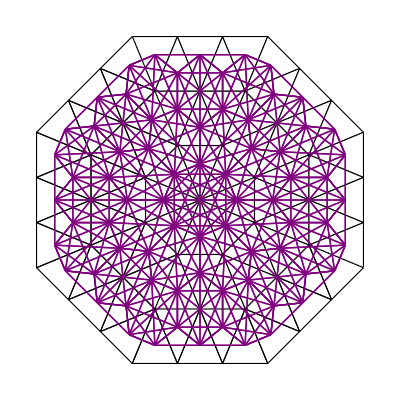

```mathematica
displayBoardWithConnections[board]
```

### Other

```mathematica
ModelToView[board_]:= 

Module[
{graphics = {},x,y},
	For[x=1,x≤ 30,x++,
						AppendTo[graphics,{}];
						For[y = 1,y≤ 16,y++,
							If[board⟦x⟧⟦y⟧⟦1⟧=== Red,
							AppendTo[graphics,{Red,Circle[{y+0.5,x-0.5},0.5]}],
							AppendTo[graphics,{Blue,Circle[{y+0.5,x-0.5},0.5],Black,Text[board⟦x⟧⟦y⟧⟦1⟧,{y+0.5,x-0.5}]}]
							]
						
						]
					];
				Return[graphics];
					
					
					


				]
```

```mathematica
minesweeperBoard[]:= Module[
{minecount,row,section,x,y},
(*Mine, status, probability*)
(*Red are mines*)

For[x = 2,x ≤ 29,x++,
For[y = 2,y≤ 15,y++,
If[board⟦x⟧⟦y⟧⟦1⟧ == Blue,
	board⟦x⟧⟦y⟧⟦1⟧ = borderingMines[board,x,y];
	(*riskMap[x,y];*)
	]
	]
];
Return[Null];

]
```

```mathematica
borderingMines[x_,y_]:= Module[{count = 0,X,Y},
						For[X = x-1,X ≤ x+1,X++,
							For[Y = y-1,Y≤ y+ 1,Y++,
								If[board⟦X⟧⟦Y⟧⟦1⟧ == Red,
								count++;
								]
							]
						];
						Return[count];
						]
```

```mathematica
riskMap[x_,y_]:= Module[{count,X,Y},
					count = borderingMines[x,y];
				For[X = x-1,X ≤ x+1,X++,
							For[Y = y-1,Y≤ y+ 1,Y++,
								
								board⟦X⟧⟦Y⟧⟦3⟧  += count/9;
								
							]
						];

]
```

```mathematica
click[x_,y_]:= Module[{},
				If[board⟦x⟧⟦y⟧⟦1⟧=== Red,

				Print["game over"],
				board⟦x⟧⟦y⟧⟦2⟧ = 1
				
					];
				


				]
```

```mathematica
minesweeperBoard[]
board
```

$Aborted[]